```mathematica
calibratingTable=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab522/04_10_2018/clb_tbl_1.csv"]
```

{{Êàëèáðîâî÷íàÿ òàáëèöà},{äëèíà âîëíû | íîìåð ïèêñåëÿ | ïîãð. íîìåðà ïèêñåëÿ},{.00},{4916.04,703.93,0.815763},{4960.32,780.374,1.55008},{5025.64,888.13,1.40821},{5045.82,920.305,1.55534},{5121.55,1037.08,1.50279},{5316.69,1306.8,1.16125},{5354.05,1356.52,1.67356},{5365.06,1369.4,1.63941},{5384.7,1394.32,1.15862},{5460.74,1485.18,2.20296},{5675.86,1719.21,1.37143},{5769.59,1812.27,2.93727},{5790.65,1832.35,3.55205},{5803.65,1844.65,1.22956},{5859.38,1896.44,1.02857},{5872.03,1907.94,1.38325},{5888.94,1923.83,1.20591},{6072.64,2077.89,1.60525},{6123.27,2118.27,1.35829},{6234.37,2202.11,1.48177}}

```mathematica
calibratingTablePlot=Transpose[RotateLeft[Delete[Transpose[calibratingTable[[4;;All]]],3],1]]
```

{{703.93,4916.04},{780.374,4960.32},{888.13,5025.64},{920.305,5045.82},{1037.08,5121.55},{1306.8,5316.69},{1356.52,5354.05},{1369.4,5365.06},{1394.32,5384.7},{1485.18,5460.74},{1719.21,5675.86},{1812.27,5769.59},{1832.35,5790.65},{1844.65,5803.65},{1896.44,5859.38},{1907.94,5872.03},{1923.83,5888.94},{2077.89,6072.64},{2118.27,6123.27},{2202.11,6234.37}}

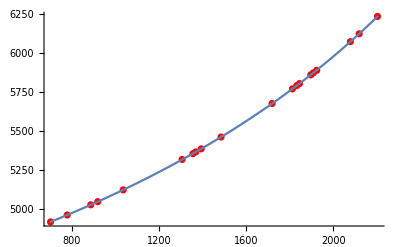

```mathematica
Show[ListPlot[calibratingTablePlot,PlotStyle->Red],Plot[2510.01+(-1.01864*10^7)/(x-4937.46),{x,700,2205}]]
```

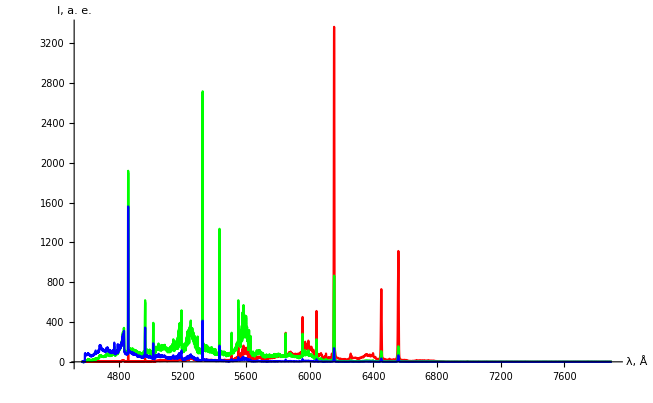

```mathematica
spectre=Import["/Users/alex/Library/Mobile Documents/com~apple~CloudDocs/Лабы/Labs/Phys_Labs/5_sem/Lab522/04_10_2018/h2_1.csv"];
spectrePlot=spectre[[3;;All]];
SpectreImage=Show[
ListLinePlot[Transpose[{spectrePlot[[All,1]]}].({{1, 0}})+Transpose[{spectrePlot[[All,2]]}].({{0, 1}}),PlotRange->All,PlotStyle->Red],
ListLinePlot[Transpose[{spectrePlot[[All,1]]}].({{1, 0}})+Transpose[{spectrePlot[[All,3]]}].({{0, 1}}),PlotRange->All,PlotStyle->Green],
ListLinePlot[Transpose[{spectrePlot[[All,1]]}].({{1, 0}})+Transpose[{spectrePlot[[All,4]]}].({{0, 1}}),PlotRange->All,PlotStyle->Green],
ListLinePlot[Transpose[{spectrePlot[[All,1]]}].({{1, 0}})+Transpose[{spectrePlot[[All,5]]}].({{0, 1}}),PlotRange->All,PlotStyle->Blue],LabelStyle->{GrayLevel[0]},
AxesLabel->{HoldForm["λ, Å"],HoldForm["I, a. e."]},PlotLabel->None
]
```

```mathematica
spectrePlotUnified=spectrePlot[[All,1;;2]];
For[i=1,i≤Length[spectrePlotUnified],i++,
spectrePlotUnified[[i,2]]=Max[spectrePlot[[i,2;;5]]];
]
```

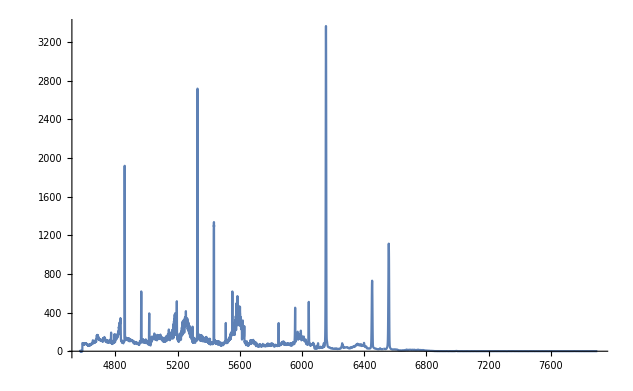

```mathematica
ListLinePlot[spectrePlotUnified,PlotRange->All]
```

```mathematica
Peaks=PeakDetect[Transpose[spectrePlotUnified][[2]]]
```

{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,30315,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0}
 |  |  |  |

```mathematica
PeaksCoords=DeleteCases[MapThread[And,{spectrePlotUnified,Peaks/.{1->True, 0->False}}],False];
```

```mathematica
For[i=1,i≤Length[PeaksCoords],i++,
If[PeaksCoords[[i,2]]<700,
PeaksCoords[[i]]=0;
];
]
PeaksCoords=DeleteCases[PeaksCoords,0];
```

```mathematica
PeaksCoords
```

{{4860.5,1918.2},{5328.18,2716.69},{5434.16,1335.84},{6154.2,3363.92},{6450.97,729.517},{6557.78,1112.86}}

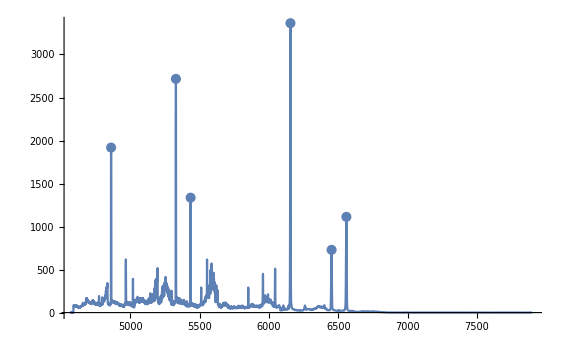

```mathematica
Show[ListLinePlot[spectrePlotUnified,PlotRange->All],ListPlot[PeaksCoords]]
```

```mathematica
Grid[Transpose[PeaksCoords]]
```

4860.5 | 5328.18 | 5434.16 | 6154.2 | 6450.97 | 6557.78
1918.2 | 2716.69 | 1335.84 | 3363.92 | 729.517 | 1112.86

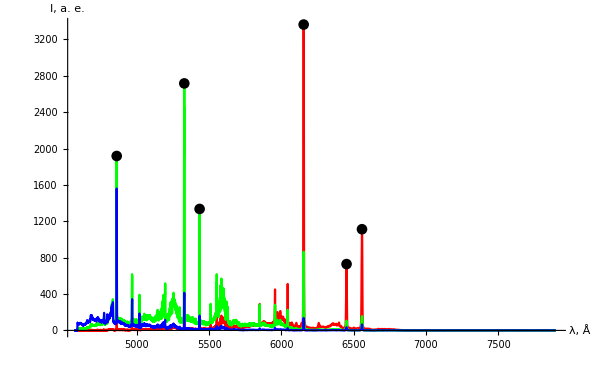

```mathematica
Show[SpectreImage,ListPlot[PeaksCoords,PlotStyle->Black]]
```

```mathematica
TeXForm[Grid[Transpose[PeaksCoords]]]
```

\begin{array}{cccccc}
 4860.5 & 5328.18 & 5434.16 & 6154.2 & 6450.97 & 6557.78 \\
 1918.2 & 2716.69 & 1335.84 & 3363.92 & 729.517 & 1112.86 \\
\end{array}